```mathematica
A={{1,0},{0,1},{-Sqrt[1-0.1^2],-0.1}};
suppA[p_]:=Max[A.p];
Manipulate[{
Graphics[{{FaceForm[White],EdgeForm[Black],Simplex[A]},Circle[{x1,x2},t]}],
Plot[{x1,x2}.{Cos[ϕ],Sin[ϕ]}+t-suppA[{Cos[ϕ],Sin[ϕ]}],{ϕ,0,2π},ImageSize->Large,AxesLabel->{"ϕ","(p,x) + t * s(p,B) - s(p,A)"}]
},{{x1,0},-2,2},{{x2,0},-1,1},{{t,1},0,2}]
```

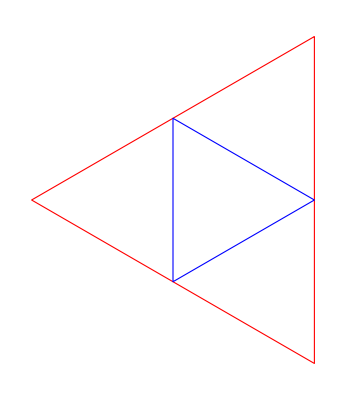
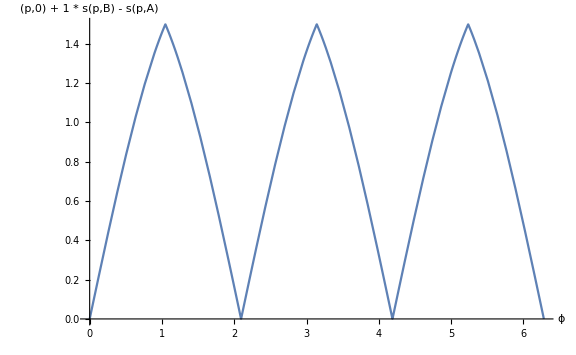

```mathematica
A={{1,0},{-1/2,Sqrt[3]/2},{-1/2,-Sqrt[3]/2}};
B={{1,Sqrt[3]},{-2,0},{1,-Sqrt[3]}};
supp[angle_,vertices_]:=Max[vertices.{Cos[angle],Sin[angle]}];
{Graphics[{{FaceForm[White],EdgeForm[Red],Simplex[B]},{FaceForm[White],EdgeForm[Blue],Simplex[A]}}],
Plot[supp[ϕ,B]-supp[ϕ,A],{ϕ,0,2π},ImageSize->Large,AxesLabel->{"ϕ","(p,0) + 1 * s(p,B) - s(p,A)"}]}
```